```mathematica
Needs["PlotLegends`"]
```

```mathematica
Clear["`*"]
```

# Spencer Lyon

## Physics 330 Exam 1

### a.)

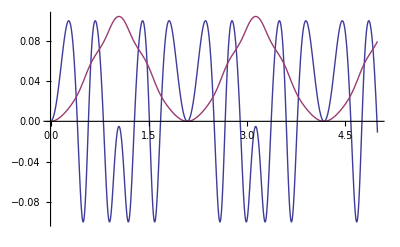

-0.050741

```mathematica
m = 3; R = 0.1; L = 0.1; θ = π / 3;g = 9.8;kk = 40;
s = ((L + R * ϕ[t] + R* Sin[ϕ[t]])^2 + (R - R * Cos[ϕ[t]])^2)^(1/2);
u = R/(s + L)*((L + R*ϕ[t]) * (1 + Cos[ϕ[t]]) + 2*R*Sin[ϕ[t]]);
lhs = 3/2 m R^2 ϕ''[t];
rhs = m g R Sin[θ] - k*s*u;
sol = NDSolve[{(lhs==rhs)/.k->kk, ϕ[0]==0, ϕ'[0]==0}, ϕ[t], {t, 0, 40}];
Plot[{R * Sin[ϕ[t]/.sol],(ϕ[t]/.sol)/120}, {t, 0, 5}, PlotRange->All, PlotLegend->{"x(t)", "ϕ(t)/120" }, LegendPosition->{-1.3,-1.3}]
FindMaximum[ϕ[t]/.sol, {t, 0, 2}][[1]] - 4 π
```

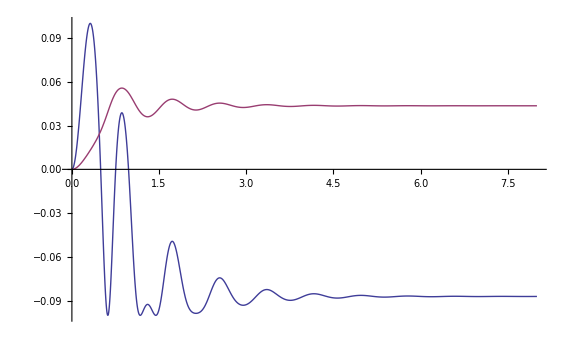

```mathematica
m = 3; R = 0.1; L = 0.1; θ = π / 3;g = 9.8;kk = 40; b = 1;
s = ((L + R * ϕ[t] + R* Sin[ϕ[t]])^2 + (R - R * Cos[ϕ[t]])^2)^(1/2);
u = R/(s + L)*((L + R*ϕ[t]) * (1 + Cos[ϕ[t]]) + 2*R*Sin[ϕ[t]]);
lhs = 3/2 m R^2 ϕ''[t];
rhs = m g R Sin[θ] - k*s*u - b R ϕ'[t];
sol = NDSolve[{(lhs==rhs)/.k->kk, ϕ[0]==0, ϕ'[0]==0}, ϕ[t], {t, 0, 40}];
Plot[{R * Sin[ϕ[t]/.sol],(ϕ[t]/.sol)/120}, {t, 0, 8}, PlotRange->All]
```

We can see from above that x_e is just a little above -0.10 (probably around -0.087).

Also note that the blue line is the position of the disk and the magenta colored line is the angle ϕ.